# Col1_BaWM_005

```mathematica
SetOptions[$FrontEnd,Background->LightYellow,FontColor->Black]
```

## Initialise

```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]]
```

#### Define plotting functions:

```mathematica
imsize=10^2.95;
Directory[]
SetDirectory[NotebookDirectory[]]
arrowParametricPlot[f_List,p_List,opts:OptionsPattern[]]:=Block[{delta=(p[[3]]-p[[2]])/1000.},ParametricPlot[f,p,Evaluate[FilterRules[{opts},Options[ParametricPlot]]],Epilog->{Arrowheads[.1,0],Arrow[{f/.p[[1]]->p[[3]]-#-delta,f/.p[[1]]->p[[3]]-#}&/@{0,(p[[3]]-p[[2]])/4,(p[[3]]-p[[2]])/2,3(p[[3]]-p[[2]])/4}]},PlotRange->All]]/;Length[f]==2&&Length[p]==3&&!FreeQ[f[[1]],p[[1]]]&&!FreeQ[f[[2]],p[[1]]];
TwoAxisPlot[{f_,g_},{x_,x1_,x2_},{xlabel_,flabel_,glabel_},tticks_,opts:OptionsPattern[]]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#[[1]],{x,x1,x2},Axes->True,PlotStyle->{ColorData[1][#2[[1]]],AbsoluteThickness[5]},LabelStyle->Directive[24],ImageSize->2^10,Evaluate[FilterRules[{opts},Options[Plot]]]]&,{{f,flabel},{g,glabel}}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,5],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameLabel->{{Style[flabel,Bold,40,ColorData[1][1]],Style[glabel,Bold,40,ColorData[1][2]]},{Style[xlabel,Bold,40,ColorData[1][2]],}},FrameTicks->{{fticks,gticks},{tticks,Automatic}}]]
TwoAxisListLinePlot[{f_,g_},{flabel_,glabel_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListLinePlot[#[[1]],Axes->True,PlotStyle->{ColorData[1][#2[[1]]],Thickness[0.005]},LabelStyle->Directive[18],ImageSize->2^10]&,{{f,flabel},{g,glabel}}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameLabel->{{Style[flabel,Bold,20,ColorData[1][1]],Style[glabel,Bold,20,ColorData[1][2]]},{,}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

## Run model

#### Load variables and set parameters:

```mathematica
(*Pulse*)
pulse[x_]:=((Cos[Exp[-1]]-Cos[Exp[Cos[(Pi/12)x]]])/(Cos[Exp[-1]]-Cos[E]))^4;
circCos[t_,ph_,per_,amp_,mean_]:=0.5amp Cos[(2Pi/per)(t-ph)]+mean;
intFac=(1/24)NIntegrate[((Cos[Exp[-1]]-Cos[Exp[Cos[(Pi/12)x]]])/(Cos[Exp[-1]]-Cos[E]))^4,{x,0,24}];
pulse2[t_,ph_,per_,mean_]:=(mean/intFac)((Cos[Exp[-1]]-Cos[Exp[Cos[(2Pi/per)(t-ph) ]]])/(Cos[Exp[-1]]-Cos[E]))^4;

(*Plot[{pulse[t],pulse2[t,0,24,1],circCos[t,0,24,1,1],Evaluate[D[pulse[t],t]]},{t,0,72},PlotLabels->{pulse[t],pulse2[t,0,24,1],circCos[t,0,24,1,1],D[pulse[t],t]},PlotStyle->Thickness[0.01],PlotRange->All,ImageSize->2^10]*)

(*Variables:*)
variables={pCER[t],pCH[t],pCG[t],pCPG[t],pCPM[t],pCE[t],pHER[t],pHG[t],pPk[t]};
dX={pCER'[t],pCH'[t],pCG'[t],pCPG'[t],pCPM'[t],pCE'[t],pHER'[t],pHG'[t],pPk'[t]};
colVars={pCER[t],pCH[t],pCG[t],pCPG[t],pCPM[t],pCE[t]};
inputs={pS[t],pT[t],pPd[t],pV[t],pM[t],pD[t]};
inputNames={"pS[t]","pT[t]","pPd[t]","pV[t]","pM[t]","pD[t]"};

initCons=Table[(variables[[i]]/.t->0)==0,{i,Length[variables]}];

(*Parameter functions:*)
tspan =24000;
uMMed=0.0342;
hMed=24;

k1=0.00822; (*pS concentration*)
(*k1a=0.00029;(*S synthesis*)
k1b=Log[2]/51.43; (*S degradation*)*)
k2=0.0105; (*pT concentration*)
(*k2a=0.0844; (*T synthesis (see notes 20171102)*)
k2b=Log[2]/57.61; (*T degradation*)*)
k3=0.0342; (*pPd concentration (median)*)
(*k3a=0.201; (*pPd synthesis (median rate)*)
k3b=Log[2]/47.91; (*pPd degradation (median rate)*)*)
k4a=.1*0.398/k1; (*H synthesis - .1 added to make levels physical 20181212*)
k4b=Log[2]/167.68; (*H degradation*)
k4c=Log[2]/167.68; (*H degradation*)
k5a=0.0155/k1; (*pPk synthesis*)
k5b=Log[2]/100.47; (*pPk degradation*)
k5c=uMMed^(-1); (*pPk represssion constant*)
k6=0.00335; (*pV concentration*)
(*k6a=0.0137; (*V synthesis*)
k6b=Log[2]/71.97; (*V degradation*)*)
k7=0.00457; (*M concentration*)
(*k7a=0.0923; (*M synthesis*)
k7b=Log[2]/4.82; (*M degradation*)*)
k8=.01(0.057+0.029)/k1; (*pCER synthesis - .01 added to make levels physical 20181212   h^-1 when feedb=0*)
(*(****)k9=1.; (**** pCER+T+pHER->pCH+T   uM^-2 h^-1*)
(****)k10=10.; (**** pCH->pHG+pCG   h^-1*)
(****)k11=1.; (**** pCG+V->pCPG+V   uM^-1 h^-1*)
(****)k12=1.; (**** pCPG->pCPM   h^-1*) 
(****)k13=1.; (**** pCPM+M->pCE+M   uM^-1 h^-1*)
(****)k14=1.;(*** pCE degradation   uM^-1 h^-1*)*)
(****)k9=0.01(uMMed^-2)(hMed^-1); (**** pCER+T+pHER->pCH+T   uM^-2 h^-1*)
(****)km9=(uMMed^-1)(hMed^-1);(**** pCER+T+pHER<-pCH+T   uM^-1 h^-1*)
(****)k10=24*60*60(hMed^-1); (**** pCH->pHG+pCG   h^-1*)
(****)k11=(uMMed^-1)(hMed^-1); (**** pCG+V->pCPG+V   uM^-1 h^-1*)
(****)k12=(hMed^-1); (**** pCPG->pCPM   h^-1*) 
(****)k13=(*10.*)(uMMed^-1)(hMed^-1); (**** pCPM+M->pCE+M   uM^-1 h^-1*)
(****)k14=(uMMed^-1)(hMed^-1);(*** pCE degradation   uM^-1 h^-1*)
k15=uMMed; (*pD concentration (median)*)
(*k15a=0.201; (*CTSK synthesis (median rate)*)
k15b=Log[2]/47.91; (*CTSK degradation (median rate)*)*)
(****)k16=(uMMed^-1)(hMed^-1); (**** pHG+pK->pHER+K   uM^-1 h^-1*)
(****)k17=0.013;
(****)hill=3.;
(*(****)act=0.1;*)

If[Length[variables]==Length[dX],Print["VarNum lengths match up"],Print[Style["ERROR VarNum",18,Red]]]
```

#### Clockless run (run the model without oscillations, i.e. osc=0)

0.0499274

2.675649

pCER[t] | pCH[t] | pCG[t] | pCPG[t] | pCPM[t] | pCE[t] | pHER[t] | pHG[t] | pPk[t]
0.0238816
t→23992.9 | 2.38889×10^-7
t→23999.4 | 0.210713
t→23999.4 | 0.02064
t→23999.4 | 0.154461
t→23986.2 | 0.02064
t→23977.8 | 9.62744
t→23999.4 | 0.000626489
t→23999.4 | 1.12334
t→23999.4
0.0238816
t→23999.4 | 2.38889×10^-7
t→23999.4 | 0.210713
t→23999.4 | 0.02064
t→23999.4 | 0.154461
t→23986.2 | 0.02064
t→23977.8 | 9.62744
t→23999.4 | 0.000626489
t→23999.4 | 1.12334
t→23999.4
1.45277×10^-14 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.409696 |  |  |  |  |  |  |  | 
0.409696 |  |  |  |  |  |  |  |

pS[t] | pT[t] | pPd[t] | pV[t] | pM[t] | pD[t]
0.01233
t→23979. | 0.0508322
t→23985. | 0.0513
t→23995. | 0.005025
t→23995. | 0.0221241
t→23979. | 0.0513
t→23985.
0.00411
t→23991. | 1.60509×10^-43
t→23997. | 0.0171
t→23983. | 0.001675
t→23983. | 4.57138×10^-60
t→23991. | 0.0171
t→23997.
66.6667 | 100. | 66.6667 | 66.6667 | 100. | 66.6667

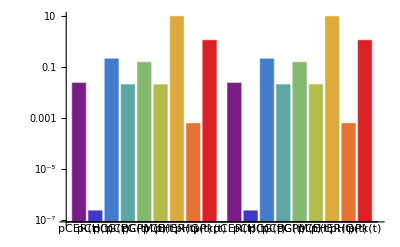

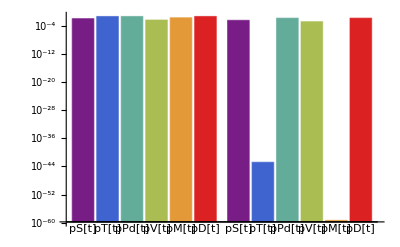

4.5205383

```mathematica
osc=0;
feedb=0;
deg=1;
(* Protein concentrations*)
pS[t]=osc*k1 circCos[t,3.,24,1,1](**pulse[3.+t-3.]*)+(1-osc)k1; (*Sec61a*)
pT[t]=osc*k2(**0.5(Cos[(Pi/12)(6.+t-9.)]+1.)*)*pulse2[t,9.,24,1]+(1-osc)k2; (*TANGO*)
pPd[t]=osc*k3 circCos[t,19.,24,1,1](**pulse[3.+t-19.]*)+(1-osc)k3; (*PDE4D*)
pV[t]=osc*k6 circCos[t,19.,24,1,1](**pulse[3.+t-19]*)+(1-osc)k6; (*VPS33b*)
pM[t]=osc*k7(**0.5(Cos[(Pi/12)(6.+t-3.)]+1.)*)*pulse2[t,3.,24,1]+(1-osc)k7; (*MMP14*)
pD[t]=deg(osc*k15 circCos[t,9.,24,1,1](**pulse[3.+t-9.]*)+(1-osc)k15); (*Cathepsin K*)

dXdt[1]=feedb*k8*pS[t]/(1.+((pCE[t])/k17)^hill)+(1-feedb)k8*pS[t]-k9*pCER[t]pT[t]pHER[t]+km9 pCH[t]pT[t]; (*ER collagen*)
dXdt[2]=k9*pCER[t]pT[t]pHER[t]-km9 pCH[t]pT[t]-k10*pCH[t]; (*Collagen/HSP47 ERGIC complex*)
dXdt[3]=k10*pCH[t]-k11*pCG[t]pV[t]; (*Golgi collagen*)
dXdt[4]=k11*pCG[t]pV[t]-k12*pCPG[t]; (*PGC collagen*)
dXdt[5]=k12*pCPG[t]-k13*pCPM[t]pM[t]; (*PM collagen*)
dXdt[6]=k13*pCPM[t]pM[t]-k14*pD[t]pCE[t]; (*ECM secreted collagen*)
dXdt[7]=k4a*pS[t]-k4b*pHER[t]-k9*pCER[t]pT[t]pHER[t]+km9 pCH[t]pT[t]+k16*pHG[t]pPk[t]; (*ER HSP47*)
dXdt[8]=k10*pCH[t]-k16*pHG[t]pPk[t]-k4c*pHG[t]; (*Golgi HSP47*)
dXdt[9]=k5a*pS[t]/(1+k5c pPd[t])-k5b*pPk[t]; (*PKA*)

time=AbsoluteTime[];
noClocksol1=Flatten[NDSolve[Join[Table[dX[[i]]==dXdt[i],{i,Length[dX]}],initCons],variables,{t,0,tspan},MaxSteps->Infinity,AccuracyGoal->20],1];
noClocksol=Flatten[NDSolve[Join[Table[dX[[i]]==dXdt[i],{i,Length[dX]}],initCons],variables[[;;,0]],{t,0,tspan},MaxSteps->Infinity,AccuracyGoal->20],1];
noClockresiduals=Table[dX[[i]]-dXdt[i],{i,Length[dX]}];
noClocksol1Grads=noClocksol1[[#,2,0]]'[t]&/@Range[Length[noClocksol1]];
noClocksolGrads=noClocksol[[#,2,0]]'[t]&/@Range[Length[noClocksol]];
AbsoluteTime[]-time
noClockvarMax=NMaximize[{noClocksol1[[#,2]], tspan-24≤t≤tspan},t]&/@Range[Length[variables]];
noClockvarMin=NMinimize[{noClocksol1[[#,2]], tspan-24≤t≤tspan},t]&/@Range[Length[variables]];
noClockinpMax=Maximize[{inputs[[#]], tspan-24≤t≤tspan},t]&/@Range[Length[inputs]];
noClockinpMin=Minimize[{inputs[[#]], tspan-24≤t≤tspan},t]&/@Range[Length[inputs]];
AbsoluteTime[]-time
noClockgradMax=NMaximize[{noClocksol1Grads[[#]], tspan-24≤t≤tspan},t]&/@Range[Length[variables]];
noClockgradMin=NMinimize[{noClocksol1Grads[[#]], tspan-24≤t≤tspan},t]&/@Range[Length[variables]];
noClocksolCE1Day=noClocksol[[Position[variables,pCE[t]][[1,1]],2]]-noClocksol[[Position[variables,pCE[t]][[1,1]],2,0]][tspan-24];
{variables,noClockvarMax,noClockvarMin,100(noClockvarMax[[;;,1]]-noClockvarMin[[;;,1]])/noClockvarMax[[;;,1]],Total[noClockvarMax[[1;;5,1]]],Total[noClockvarMin[[1;;5,1]]]}//TableForm
{inputNames,noClockinpMax,noClockinpMin,100(noClockinpMax[[;;,1]]-noClockinpMin[[;;,1]])/noClockinpMax[[;;,1]]}//TableForm
BarChart[(*Partition[Riffle[varMax[[;;,1]],varMin[[;;,1]]],2]*){noClockvarMax[[;;,1]],noClockvarMin[[;;,1]]},ChartLabels->variables,ChartStyle->"Rainbow",ScalingFunctions->"Log"]
BarChart[(*Partition[Riffle[varMax[[;;,1]],varMin[[;;,1]]],2]*){noClockinpMax[[;;,1]],noClockinpMin[[;;,1]]},ChartLabels->inputNames,ChartStyle->"Rainbow",ScalingFunctions->"Log"]
AbsoluteTime[]-time
```

#### Solve the system, with osc=1:

30.981383

132.609571

pCER[t] | pCH[t] | pCG[t] | pCPG[t] | pCPM[t] | pCE[t] | pHER[t] | pHG[t] | pPk[t]
0.0310526
t→23981.7 | 1.20013×10^-6
t→23984.3 | 0.218508
t→23988.2 | 0.0222851
t→23976.2 | 0.161235
t→23999.7 | 0.0274715
t→23981.8 | 9.7013
t→23984.9 | 0.00276014
t→23985. | 1.21824
t→23985.9
0.0174053
t→23988.5 | -1.30595×10^-22
t→23996.9 | 0.202484
t→23981. | 0.0189845
t→23988.1 | 0.147881
t→23982.3 | 0.0139897
t→23998.9 | 9.55206
t→23996.9 | 3.36212×10^-10
t→23999.5 | 1.17755
t→23998.6
43.9491 | 100. | 7.33332 | 14.811 | 8.28217 | 49.0756 | 1.5384 | 100. | 3.33984
0.433082 |  |  |  |  |  |  |  | 
0.386755 |  |  |  |  |  |  |  |

pS[t] | pT[t] | pPd[t] | pV[t] | pM[t] | pD[t]
0.01233
t→23979. | 0.0508322
t→23985. | 0.0513
t→23995. | 0.005025
t→23995. | 0.0221241
t→23979. | 0.0513
t→23985.
0.00411
t→23991. | 1.60509×10^-43
t→23997. | 0.0171
t→23983. | 0.001675
t→23983. | 4.57138×10^-60
t→23991. | 0.0171
t→23997.
66.6667 | 100. | 66.6667 | 66.6667 | 100. | 66.6667

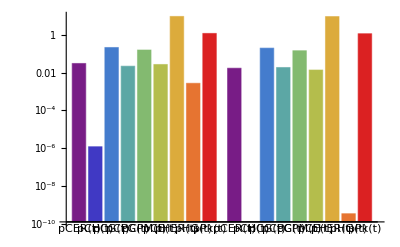

-Graphics-

232.008409

```mathematica
osc=1;
feedb=0;
deg=1;
(* Protein concentrations*)
pS[t]=osc*k1(0.5Cos[(Pi/12)(t-3.)]+1.)(**pulse[3.+t-3.]*)+(1-osc)k1; (*Sec61a*)
pT[t]=osc*k2(**0.5(Cos[(Pi/12)(6.+t-9.)]+1.)*)*pulse2[t,9.,24,1]+(1-osc)k2; (*TANGO*)
pPd[t]=osc*k3(0.5Cos[(Pi/12)(t-19.)]+1.)(**pulse[3.+t-19.]*)+(1-osc)k3; (*PDE4D*)
pV[t]=osc*k6(0.5Cos[(Pi/12)(t-19.)]+1.)(**pulse[3.+t-19]*)+(1-osc)k6; (*VPS33b*)
pM[t]=osc*k7(**0.5(Cos[(Pi/12)(6.+t-3.)]+1.)*)*pulse2[t,3.,24,1]+(1-osc)k7; (*MMP14*)
pD[t]=deg(osc*k15(0.5Cos[(Pi/12)*(t-9.)]+1.)(**pulse[3.+t-9.]*)+(1-osc)k15); (*Cathepsin K*)

dXdt[1]=feedb*k8*pS[t]/(1.+((pCE[t])/k17)^hill)+(1-feedb)k8*pS[t]-k9*pCER[t]pT[t]pHER[t]+km9 pCH[t]pT[t]; (*ER collagen*)
dXdt[2]=k9*pCER[t]pT[t]pHER[t]-km9 pCH[t]pT[t]-k10*pCH[t]; (*Collagen/HSP47 ERGIC complex*)
dXdt[3]=k10*pCH[t]-k11*pCG[t]pV[t]; (*Golgi collagen*)
dXdt[4]=k11*pCG[t]pV[t]-k12*pCPG[t]; (*PGC collagen*)
dXdt[5]=k12*pCPG[t]-k13*pCPM[t]pM[t]; (*PM collagen*)
dXdt[6]=k13*pCPM[t]pM[t]-k14*pD[t]pCE[t]; (*ECM secreted collagen*)
dXdt[7]=k4a*pS[t]-k4b*pHER[t]-k9*pCER[t]pT[t]pHER[t]+km9 pCH[t]pT[t]+k16*pHG[t]pPk[t]; (*ER HSP47*)
dXdt[8]=k10*pCH[t]-k16*pHG[t]pPk[t]-k4c*pHG[t]; (*Golgi HSP47*)
dXdt[9]=k5a*pS[t]/(1+k5c pPd[t])-k5b*pPk[t]; (*PKA*)

time=AbsoluteTime[];
sol1=Flatten[NDSolve[Join[Table[dX[[i]]==dXdt[i],{i,Length[dX]}],initCons],variables,{t,0,tspan},MaxSteps->Infinity,AccuracyGoal->20],1];
sol=Flatten[NDSolve[Join[Table[dX[[i]]==dXdt[i],{i,Length[dX]}],initCons],variables[[;;,0]],{t,0,tspan},MaxSteps->Infinity,AccuracyGoal->20],1];
residuals=Table[dX[[i]]-dXdt[i],{i,Length[dX]}];
sol1Grads=sol1[[#,2,0]]'[t]&/@Range[Length[sol1]];
solGrads=sol[[#,2,0]]'[t]&/@Range[Length[sol]];
AbsoluteTime[]-time
varMax=NMaximize[{sol1[[#,2]], tspan-24≤t≤tspan},t]&/@Range[Length[variables]];
varMin=NMinimize[{sol1[[#,2]], tspan-24≤t≤tspan},t]&/@Range[Length[variables]];
inpMax=Maximize[{inputs[[#]], tspan-24≤t≤tspan},t]&/@Range[Length[inputs]];
inpMin=Minimize[{inputs[[#]], tspan-24≤t≤tspan},t]&/@Range[Length[inputs]];
AbsoluteTime[]-time
gradMax=NMaximize[{sol1Grads[[#]], tspan-24≤t≤tspan},t]&/@Range[Length[variables]];
gradMin=NMinimize[{sol1Grads[[#]], tspan-24≤t≤tspan},t]&/@Range[Length[variables]];
solCE1Day=sol[[Position[variables,pCE[t]][[1,1]],2]]-sol[[Position[variables,pCE[t]][[1,1]],2,0]][tspan-24];
{variables,varMax,varMin,100(varMax[[;;,1]]-varMin[[;;,1]])/varMax[[;;,1]],Total[varMax[[1;;5,1]]],Total[varMin[[1;;5,1]]]}//TableForm
{inputNames,inpMax,inpMin,100(inpMax[[;;,1]]-inpMin[[;;,1]])/inpMax[[;;,1]]}//TableForm
BarChart[(*Partition[Riffle[varMax[[;;,1]],varMin[[;;,1]]],2]*){varMax[[;;,1]],varMin[[;;,1]]},ChartLabels->variables,ChartStyle->"Rainbow",ScalingFunctions->"Log"]
BarChart[(*Partition[Riffle[varMax[[;;,1]],varMin[[;;,1]]],2]*){inpMax[[;;,1]],inpMin[[;;,1]]},ChartLabels->inputNames,ChartStyle->"Rainbow",ScalingFunctions->"Log"]
AbsoluteTime[]-time
```

```mathematica
(*Export["colVars_maxmin.png",Transpose[{Join[{""},variables[[1;;6]]],Join[{"Max (μM)"},varMax[[1;;6,1]]],Join[{"Min (μM)"},varMin[[1;;6,1]]]}]//TableForm]*)
```

```mathematica
paramtable=Cell[BoxData[ToBoxes[TableForm[Transpose[{Join[{""},Style[#,Italic]&/@variables[[1;;6]]],Join[{Style["Max (μM)",Bold]},NumberForm[varMax[[#,1]],3]&/@Range[6]],Join[{Style["Min (μM)",Bold]},NumberForm[varMin[[#,1]],3]&/@Range[6]]}],TableSpacing->{4,3}]]],"Output",FontFamily->"Arial"];
```

#### Residuals Plots

```mathematica
time=AbsoluteTime[];
With[{data=Table[{t,Abs@#}/.sol,{t,pCER["Coordinates"]/.sol//Flatten}]&/@residuals},ListLogPlot[#,Frame->True,PlotRange->{{tspan-24*7,tspan},All},ImageSize->2^10]&/@data]
AbsoluteTime[]-time
```

```mathematica
(pCE[tspan-12]/.sol[[Position[variables,pCE[t]][[1,1]]]])-(pCE[tspan-36]/.sol[[Position[variables,pCE[t]][[1,1]]]])
(pCE[tspan-24+#]/.sol[[Position[variables,pCE[t]][[1,1]]]])&/@Range[24]
```

1.15917×10^-11

{0.016057,0.0188704,0.022155,0.0251051,0.0270198,0.027434,0.0265956,0.025198,0.0237044,0.0222766,0.0209616,0.0197775,0.0187319,0.0178252,0.0170515,0.0164,0.0158563,0.0154027,0.0150196,0.0146861,0.0143833,0.0141139,0.0139933,0.0144398}

#### Plot collagen variables:

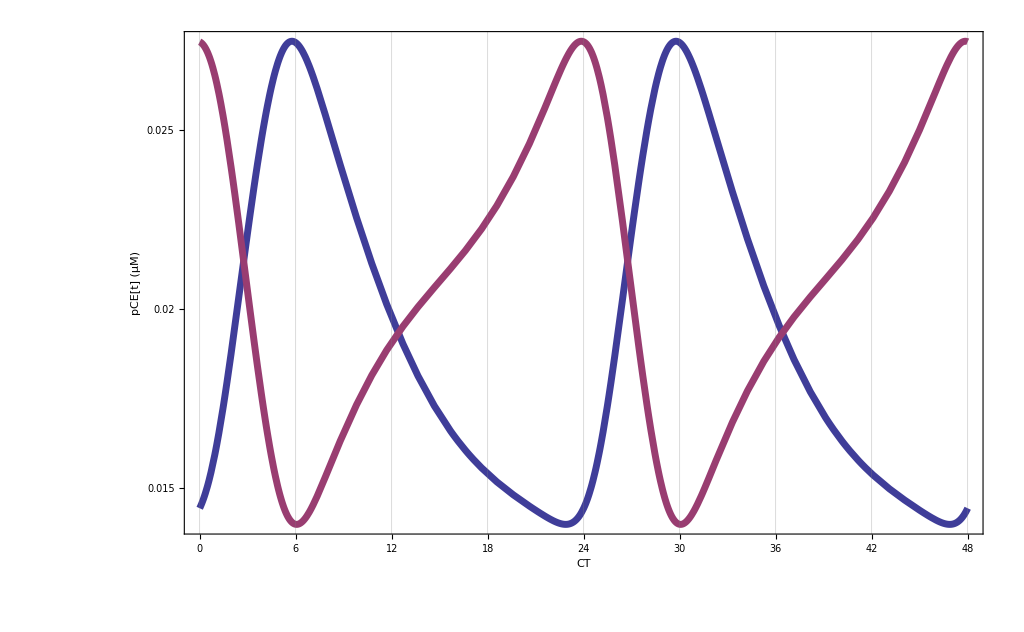

-Graphics-

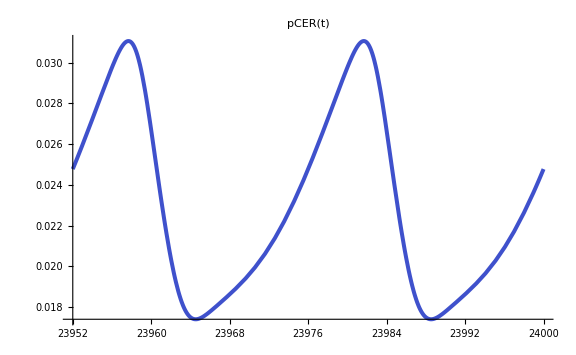
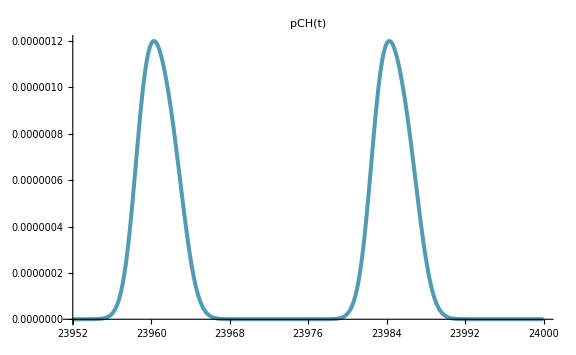
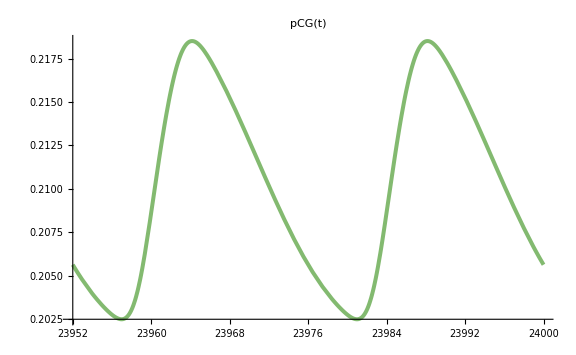
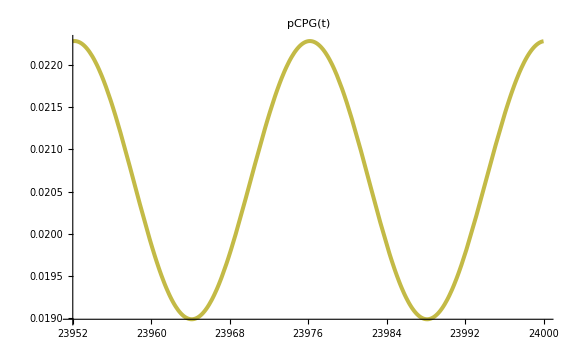
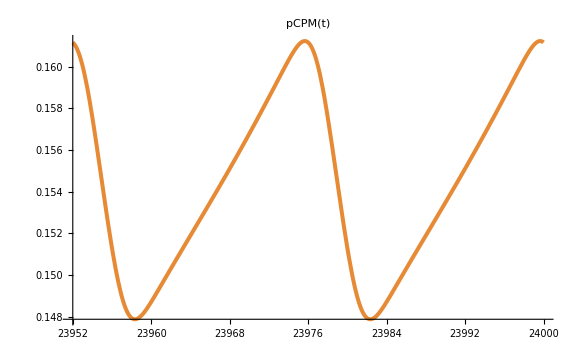
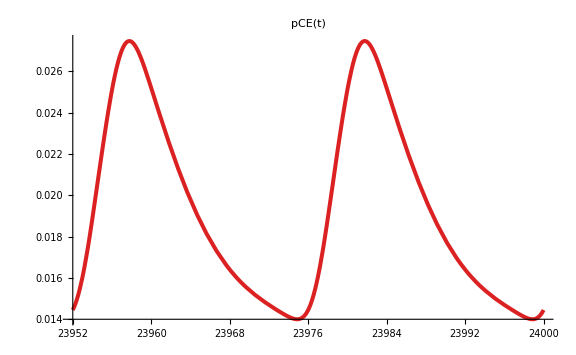

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {sol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value -48+tspan in {Charting`Private`pvar$2326,-48+tspan,tspan} is not a machine-sized real number.

Plot::plln: Limiting value -48+tspan in {Charting`Private`pvar$2411,-48+tspan,tspan} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {sol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value -48+tspan in {Charting`Private`pvar$2488,-48+tspan,tspan} is not a machine-sized real number.

Plot::plln: Limiting value -48+tspan in {Charting`Private`pvar$2523,-48+tspan,tspan} is not a machine-sized real number.

Part::partd: Part specification inputs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value -48+tspan in {Charting`Private`pvar$2575,-48+tspan,tspan} is not a machine-sized real number.

Plot::plln: Limiting value -48+tspan in {Charting`Private`pvar$2600,-48+tspan,tspan} is not a machine-sized real number.

```mathematica
pCEvpCint=TwoAxisPlot[{pCE[t]/.sol[[Position[variables,pCE[t]][[1,1]]]],Total[Table[variables[[i]]/.sol[[i]],{i,1,5}]]},{t,tspan-48,tspan},{"CT",TextString[pCE[t]]<>" (μM)","Total intracellular pC[t] (μM)"},{tspan-48+#,#}&/@{0,6,12,18,24,30,36,42,48},GridLines->{tspan-48+#&/@{0,6,12,18,24,30,36,42,48},None},PlotRangePadding->None]

varPlotsAllTime=Table[Plot[variables[[i]]/.sol[[i]],{t,0,tspan},ImageSize->Large,PlotLabel->variables[[i]],LabelStyle->Directive[18],PlotStyle->{Thickness[.005]}],{i,Length[variables]}];

Manipulate[Plot[Evaluate[var/.sol[[Position[variables,var][[1,1]]]]],{t,tspan-48,tspan},ImageSize->Large,LabelStyle->Directive[18],PlotStyle->{Thickness[.005]},Ticks->{{tspan-48+#,#}&/@{0,3,7,11,15,19,23,27,31,35,39,43,47},Automatic},GridLines->{Automatic,None},Frame->{{True,False},{True,False}},FrameLabel->{"CT","Concentration (μM)"},PlotLabel->ExpressionCell[ToString[TraditionalForm[dX[[Position[variables,var][[1,1]]]]]]<>"="<>ToString[TraditionalForm[dXdt[Position[variables,var][[1,1]]]]],PageWidth->400,TextAlignment->Center]],{var,variables}]

Manipulate[Plot[Evaluate[inputs[[inp]]],{t,tspan-48,tspan},ImageSize->Large,LabelStyle->Directive[18],PlotStyle->{Thickness[.005]},Ticks->{{tspan-48+#,#}&/@{0,3,7,11,15,19,23,27,31,35,39,43,47},Automatic},GridLines->{Automatic,None},Frame->{{True,False},{True,False}},FrameLabel->{"CT","Concentration (μM)"},PlotLabel->ExpressionCell[TraditionalForm[inputs[[inp]]],PageWidth->400,TextAlignment->Center]],{inp,Range[Length[inputs]]}]

colPlotAll48=Plot[Evaluate[#/.sol[[Position[variables,#][[1,1]]]]&/@colVars[[1;;-2]]],{t,tspan-24*2,tspan},PlotStyle->Flatten[{{Thickness[0.005],{ColorData["Rainbow"][#/6]}}&/@Range[5]},1],ImageSize->2^10,PlotLabels->Table[Style[colVars[[i]],Bold,16,Purple],{i,1,Length[colVars]-1}],LabelStyle->Directive[18],Frame->True, FrameLabel->{Style["CT",Purple,Bold,40],Style["Concentration (μM)",Purple,Bold,40]},FrameTicks->{{True,True},{{tspan-48+#,#}&/@{0,6,12,18,24,30,36,42,48},True}},GridLines->{tspan-48+#&/@{0,6,12,18,24,30,36,42,48},None},PlotRange->Full,PlotRangePadding->None]

colPlots48=Table[Plot[colVars[[i]]/.sol[[Position[variables,colVars[[i]]][[1,1]]]],{t,tspan-24*2,tspan},ImageSize->Large,PlotLabel->colVars[[i]],LabelStyle->Directive[Bold,Purple],PlotStyle->{Thickness[.005],{ColorData["Rainbow"][i/6]}}],{i,Length[colVars]}]
```

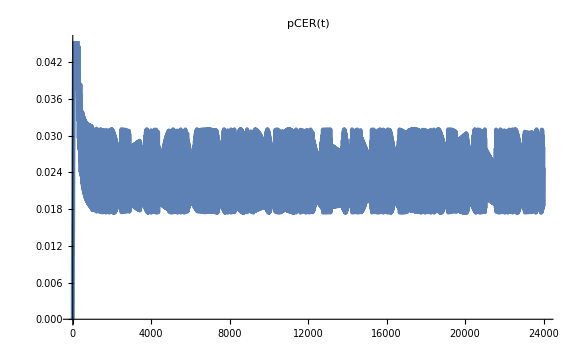
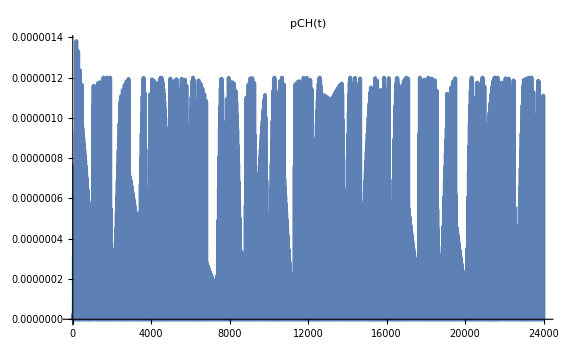
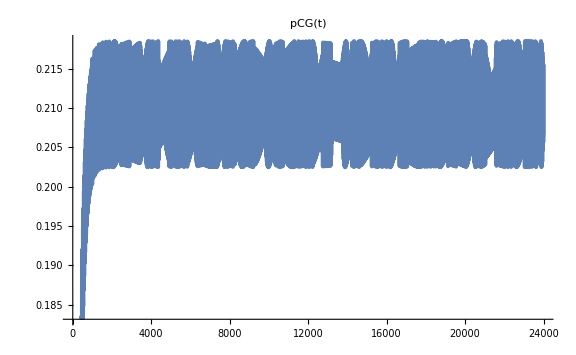
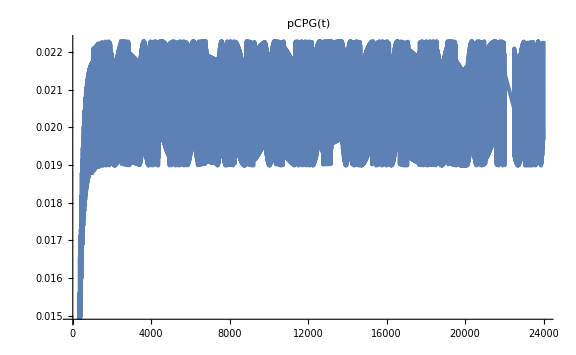
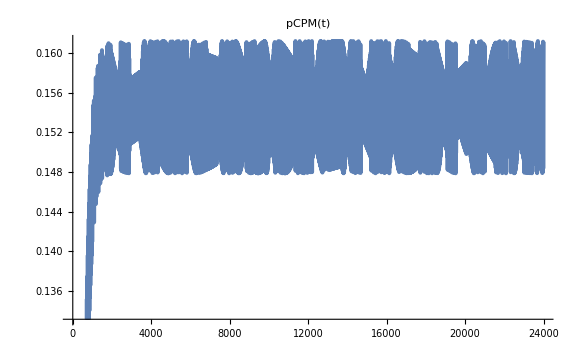
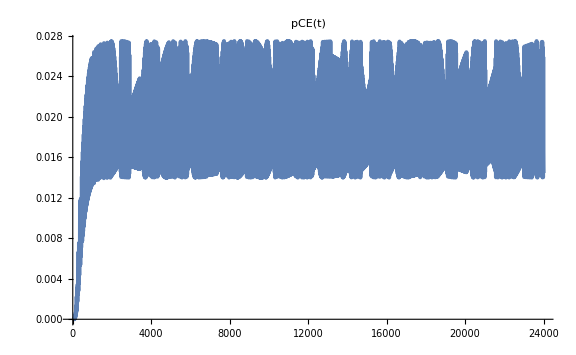
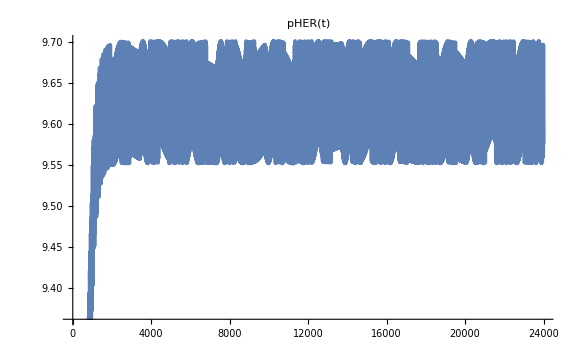
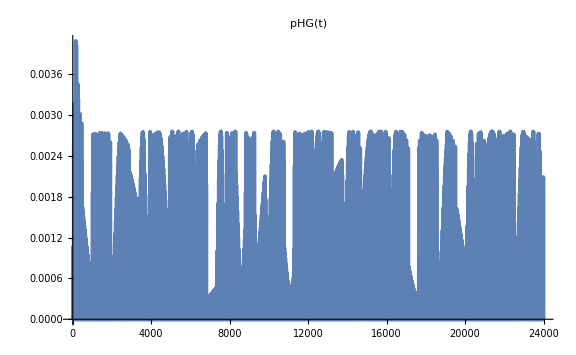

```mathematica
varPlotsAllTime
sfDy[x_]:=(x-Min[gradMin[[;;,1]]])/(Max[gradMax[[;;,1]]]-Min[gradMin[[;;,1]]])
paraColPlots=Table[Show[arrowParametricPlot[{colVars[[i]]/.sol[[Position[variables,colVars[[i]]][[1,1]]]],colVars[[j]]/.sol[[Position[variables,colVars[[j]]][[1,1]]]]},{t,tspan-24,tspan},ImageSize->2^10,PlotStyle->{Thickness[.01]},ColorFunction->Function[{x,y,t},ColorData["Rainbow"][t]],AspectRatio->1,Frame->{{True,False},{True,False}},FrameTicks->None,FrameLabel->{Style[TextString[colVars[[i]]]<>" (μM)",Purple,40,Bold],Style[TextString[colVars[[j]]]<>" (μM)",Purple,40,Bold]}],Graphics[Text[Style["✶",144,Black],#]&/@{{colVars[[i]]/.sol[[Position[variables,colVars[[i]]][[1,1]]]],colVars[[j]]/.sol[[Position[variables,colVars[[j]]][[1,1]]]]}/.t->tspan-24}],Graphics[Text[Style["✶",144,Pink],#]&/@{{colVars[[i]]/.noClocksol[[Position[variables,colVars[[i]]][[1,1]]]],colVars[[j]]/.noClocksol[[Position[variables,colVars[[j]]][[1,1]]]]}/.t->tspan-24}]],{j,1,Length[colVars]},{i,1,Length[colVars]}];

paragrid=GraphicsGrid[Table[If[i>j,paraColPlots[[i,j]]],{i,2,Length[paraColPlots]},{j,1,Length[paraColPlots]-1}]]

pCEpCintphase=Show[arrowParametricPlot[{pCE[t]/.sol[[Position[variables,pCE[t]][[1,1]]]],Total[Table[variables[[i]]/.sol[[i]],{i,1,5}]]},{t,tspan-24,tspan},ImageSize->2^10,AspectRatio->1,PlotStyle->{Thickness[.01]},ColorFunction->Function[{x,y,t},ColorData["Rainbow"][t]],Frame->{{True,False},{True,False}},FrameTicksStyle->Directive[Purple,30],FrameLabel->{Style[TextString[pCE[t]]<>" (μM)",Purple,55,Bold],Style["Total intracellular pC(t) (μM)",Purple,55,Bold]}],Graphics[Text[Style["✶",144,Black],#]&/@{{pCE[t]/.sol[[Position[variables,pCE[t]][[1,1]]]],Total[Table[variables[[i]]/.sol[[i]],{i,1,5}]]}/.t->tspan-24}],Graphics[Text[Style["✶",144,Pink],#]&/@{{pCE[t]/.noClocksol[[Position[variables,pCE[t]][[1,1]]]],Total[Table[variables[[i]]/.noClocksol[[i]],{i,1,5}]]}/.t->tspan-24}]]
```

```mathematica
Table[{variables[[i]],varMin[[i]],varMax[[i]]},{i,1,6}]//TableForm
paintPots[a_]:=Labeled[Grid[{Graphics[{{EdgeForm[Thick],ColorData[{"ThermometerColors",{Min[-gradMax[[1;;6,1]],gradMin[[1;;6,1]]],Max[-gradMin[[1;;6,1]],gradMax[[1;;6,1]]]}}][sol1Grads[[#,0]][a]],Rectangle[{-0.05,0},{0.05,((sol1[[#,2]]/.t->a)/Max[varMax[[1;;6,1]]])},RoundingRadius->.05]}},PlotLabel->Style[Framed[variables[[#]],RoundingRadius->5],Bold,20,Purple],PlotRange->{{-0.5,0.5},{-0.05,1.05}},AspectRatio->1,ImageSize->200]&/@Range[1,6]},Spacings->-8],Style["CT "<>TextString[Floor[a-tspan+24]],Purple,24],Top,ImageMargins->10];

Manipulate[paintPots[a],{a,tspan-24,tspan},ImageMargins->10,FrameMargins->Large];
Manipulate[{Animate[paintPots[a],{a,tspan-24,tspan},ImageMargins->10,FrameMargins->Large,AnimationDirection->Forward,DefaultDuration->1/speed]},{speed,0.1,0.5}]
```

pCER[t] | 0.0174053
t→23988.5 | 0.0310526
t→23981.7
pCH[t] | -1.30595×10^-22
t→23996.9 | 1.20013×10^-6
t→23984.3
pCG[t] | 0.202484
t→23981. | 0.218508
t→23988.2
pCPG[t] | 0.0189845
t→23988.1 | 0.0222851
t→23976.2
pCPM[t] | 0.147881
t→23982.3 | 0.161235
t→23999.7
pCE[t] | 0.0139897
t→23998.9 | 0.0274715
t→23981.8

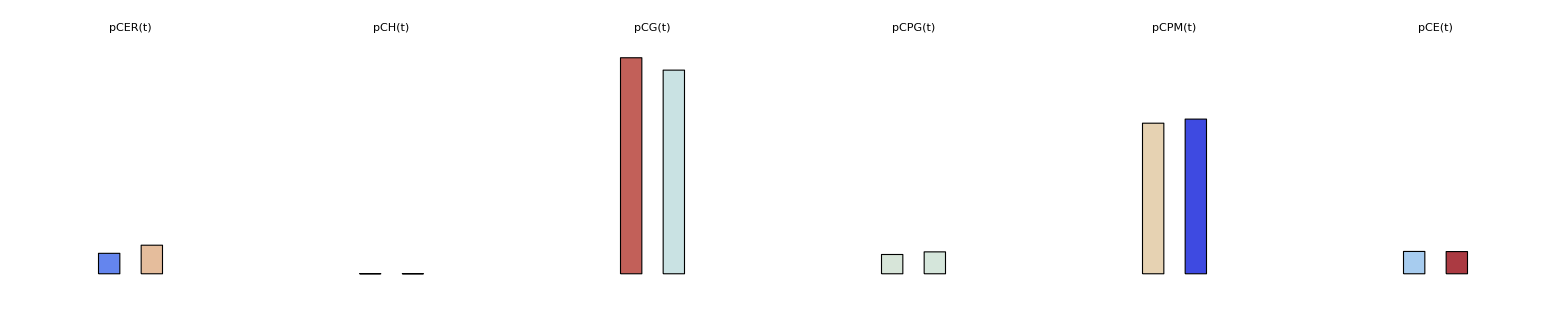
-Graphics-CT 10 & CT 3

```mathematica
paintPots2[a_,b_]:=Labeled[Grid[{Graphics[{{EdgeForm[Thick],ColorData[{"ThermometerColors",{Min[-gradMax[[1;;6,1]],gradMin[[1;;6,1]]],Max[-gradMin[[1;;6,1]],gradMax[[1;;6,1]]]}}][sol1Grads[[#,0]][a]],Rectangle[{-0.15,0},{-0.05,((sol1[[#,2]]/.t->a)/Max[varMax[[1;;6,1]]])},RoundingRadius->.05]},{EdgeForm[Thick],ColorData[{"ThermometerColors",{Min[-gradMax[[1;;6,1]],gradMin[[1;;6,1]]],Max[-gradMin[[1;;6,1]],gradMax[[1;;6,1]]]}}][sol1Grads[[#,0]][b]],Rectangle[{0.05,0},{0.15,((sol1[[#,2]]/.t->b)/Max[varMax[[1;;6,1]]])},RoundingRadius->.05]}},PlotLabel->Style[Framed[variables[[#]],RoundingRadius->5],Bold,20,Purple],PlotRange->{{-0.5,0.5},{-0.05,1.05}},AspectRatio->1,ImageSize->200]&/@Range[1,6]},Spacings->-8],Style["CT "<>TextString[Floor[a-tspan+24]]<>" & CT "<>TextString[Floor[ b-tspan+24]],Purple,24],Top,ImageMargins->10];
paintPots2[tspan-24+10,tspan-24+3]
```

## Exporting Files

#### Make sure the file names are correct before running this section.

```mathematica
time=AbsoluteTime[];
Export["colVars_maxmin.png",Notebook[{paramtable},WindowSize->500,ShowCellBracket->False],ImageSize->imsize,ImageResolution->200]
Export["pCE_Cint_48_nofeed.png",pCEvpCint,ImageResolution->200]
Export["Cints_48_nofeedb.png",colPlotAll48,ImageResolution->200]

Do[If[i≤j,Export["phase_plot_"<>TextString[i]<>"_"<>TextString[j]<>"_pulse_nofeed.png",paraColPlots[[i,j]],ImageResolution->200]],{i,1,Length[paraColPlots]},{j,1,Length[paraColPlots]}];
Export["pCintsPhase_pulse_nodiag_nofeed.png",paragrid,ImageResolution->100]
Export["pCint_pCE_phase_pulse_nofeed.png",pCEpCintphase,ImageResolution->200]

AbsoluteTime[]-time
Export["PM-ER_no_feedback_with_deg_pulse.mov",Flatten[Table[Table[paintPots[a],{a,tspan-24,tspan,0.25}],3],1]]
AbsoluteTime[]-time
Export["PM-ER_no_feedback_with_deg_pulse.avi",Flatten[Table[Table[paintPots[a],{a,tspan-24,tspan,0.25}],3],1]]
AbsoluteTime[]-time

AbsoluteTime[]-time
Export["paintpots_still_CT15.png",paintPots[tspan-9],ImageResolution->200]

Export["paintpots_CT5_+_CT17.png",paintPots2[tspan-24+5,tspan-24+17],ImageResolution->200]
Export["paintpots_CT3_+_CT15.png",paintPots2[tspan-24+3,tspan-24+15],ImageResolution->200]
AbsoluteTime[]-time
```

0.

PM-ER_no_feedback_with_deg_pulse.mov

170.926778

PM-ER_no_feedback_with_deg_pulse.avi

374.8376109

374.8456407

paintpots_still_CT15.png

paintpots_CT5_+_CT17.png

paintpots_CT3_+_CT15.png

378.4985231

## Non-dimensionalising the model

t scaling | 24
ϕ | 0.0115698
ν | 3.55344×10^-6
σ | 1/86400
ρ | 10.209
μ | 1
λ | 7.48359
ξ | 1.
χ | 10.0796
γ | 10.0796
ψ | 0.021608
θ | 14.3059
ω | 662.066
η | 6.03865
α | 1.
β | 7.6783×10^-8

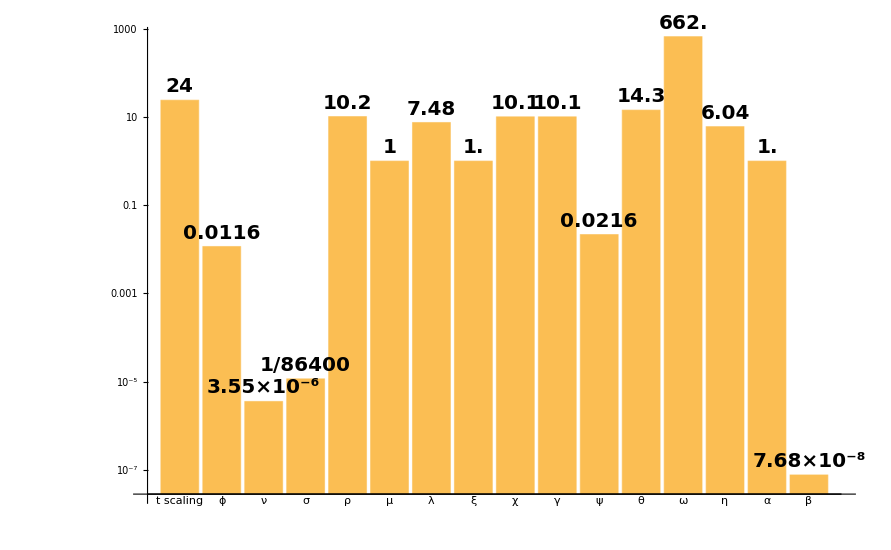

```mathematica
SetAttributes[nameVar,HoldFirst]
nameVar[var_]:=SymbolName[Unevaluated@var]

scT=24;

ϕ=k4b/(k1 k2 k4a k9 scT);
ν=k2 km9/k10;
σ=1/(k10 scT);
ρ=1/(k6 k11 scT);
μ=1/(k12 scT);
λ=1/(k7 k13 scT);
ξ=1/(k14 k15 scT);
χ=1/(k4b scT);
γ=1/(k4c scT);
ψ=k8/k4a;
θ=k1 k5a k8 k16/(k4a k4c k5b);
ω=k1 k5a k16/(k4c k5b);
η=1/(k5b scT);
α=k3 k5c;
β=k2 k8 km9/(k4a k10);

nonDimParams={scT,ϕ,ν,σ,ρ,μ,λ,ξ,χ,γ,ψ,θ,ω,η,α,β};

nonDimParamNames={"t scaling",nameVar[ϕ],nameVar[ν],nameVar[σ],nameVar[ρ],nameVar[μ],nameVar[λ],nameVar[ξ],nameVar[χ],nameVar[γ],nameVar[ψ],nameVar[θ],nameVar[ω],nameVar[η],nameVar[α],nameVar[β]};
Transpose[{nonDimParamNames,nonDimParams}]//TableForm

paramsBar=BarChart[Labeled[#,NumberForm[#,3],Above]&/@nonDimParams,ChartLabels->nonDimParamNames(*LabelingFunction->Above*),ScalingFunctions->"Log",LabelStyle->Directive[20,Bold],ImageSize->imsize]
```

0.0088416

36.6357599

36.6855533

163.923548

cer[t] | ch[t] | cg[t] | cpg[t] | cpm[t] | ce[t] | her[t] | hg[t] | k[t] | s[t] | t[t] | p[t] | v[t] | m[t] | d[t]
47.0657
t→976.147 | 10.5449
t→998.21 | 1.03185
t→982.451 | 1.07798
t→976.006 | 1.04389
t→999.986 | 1.09061
t→976.102 | 1.00782
t→981.374 | 0.0230964
t→998.228 | 0.54224
t→977.411 | 1.5
t→976.125 | 4.84116
t→981.375 | 1.5
t→985.792 | 1.5
t→985.792 | 4.84116
t→976.125 | 1.5
t→981.375
0.194347
t→985.41 | -5.17165×10^-9
t→986.909 | 0.959922
t→976.133 | 0.921871
t→993.508 | 0.957371
t→993.264 | 0.921069
t→978.599 | 0.992106
t→981.872 | 6.04938×10^-9
t→987.96 | 0.524128
t→999.941 | 0.5
t→985.625 | 5.22599×10^-35
t→981.875 | 0.5
t→997.292 | 0.5
t→997.292 | 8.88791×10^-37
t→985.625 | 0.5
t→981.875
99.5871 | 100. | 6.97086 | 14.4819 | 8.28805 | 15.5457 | 1.55944 | 100. | 3.34029 | 66.6667 | 100. | 66.6667 | 66.6667 | 100. | 66.6667
60.7643 |  |  |  |  |  |  |  |  |  |  |  |  |  | 
3.03351 |  |  |  |  |  |  |  |  |  |  |  |  |  |

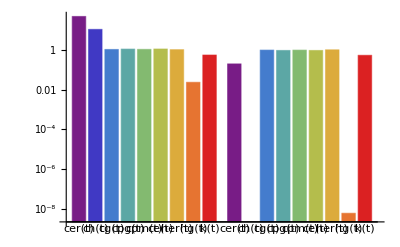

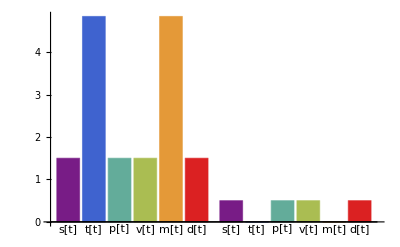

```mathematica
time=AbsoluteTime[];

(*Variables:*)
ndVars={cer[t],ch[t],cg[t],cpg[t],cpm[t],ce[t],her[t],hg[t],k[t]};
dY={cer'[t],ch'[t],cg'[t],cpg'[t],cpm'[t],ce'[t],her'[t],hg'[t],k'[t]};
ndinputs={s[t],a[t],p[t],v[t],m[t],d[t]};
ndinputNames={"s[t]","t[t]","p[t]","v[t]","m[t]","d[t]"};

ndinitCons=Table[(ndVars[[i]]/.t->0)==0,{i,Length[ndVars]}];

(*Parameter functions:*)
ndtspan =24000/scT;

s[t]=circCos[t scT,3.,24,1,1];
a[t]=pulse2[t scT,9.,24,1];
p[t]=circCos[t scT,19.,24,1,1];
v[t]=circCos[t scT,19.,24,1,1];
m[t]=pulse2[t scT,3.,24,1];
d[t]=circCos[t scT,9.,24,1,1];

(*cer*)dYdt[1]=(s[t]-cer[t]a[t]her[t]+ν ch[t]a[t])/ϕ;
(*ch*)dYdt[2]=(cer[t]a[t]her[t]-ν ch[t]a[t]-ch[t])/σ;
(*cg*)dYdt[3]=(ch[t]-cg[t]v[t])/ρ;
(*cpg*)dYdt[4]=(cg[t]v[t]-cpg[t])/μ;
(*cpm*)dYdt[5]=(cpg[t]-cpm[t]m[t])/λ;
(*ce*)dYdt[6]=(cpm[t]-d[t]ce[t])/ξ;
(*her*)dYdt[7]=(s[t]-her[t]-ψ cer[t]a[t]her[t]+β ch[t]a[t]+θ hg[t]k[t])/χ;
(*hg*)dYdt[8]=(ch[t]-ω hg[t]k[t]-hg[t])/γ;
(*k*)dYdt[9]=((s[t]/(1+α p[t]))-k[t])/η;

AbsoluteTime[]-time

ndsol=Flatten[NDSolve[Join[Table[dY[[i]]==dYdt[i],{i,Length[dY]}],ndinitCons],ndVars[[;;,0]],{t,0,ndtspan},MaxSteps->Infinity(*,AccuracyGoal->14*)],1];
ndsol1=Flatten[NDSolve[Join[Table[dY[[i]]==dYdt[i],{i,Length[dY]}],ndinitCons],ndVars,{t,0,ndtspan},MaxSteps->Infinity(*,AccuracyGoal->14*)],1];
ndresiduals=Table[dY[[i]]-dYdt[i],{i,Length[dY]}];

AbsoluteTime[]-time

ndsol1Grads=ndsol1[[#,2,0]]'[t]&/@Range[Length[ndsol1]];
ndsolGrads=ndsol[[#,2,0]]'[t]&/@Range[Length[ndsol]];

AbsoluteTime[]-time

ndvarMax=NMaximize[{ndsol1[[#,2]], ndtspan-24≤t≤ndtspan},t]&/@Range[Length[ndVars]];
ndvarMin=NMinimize[{ndsol1[[#,2]], ndtspan-24≤t≤ndtspan},t]&/@Range[Length[ndVars]];
ndinpMax=Maximize[{ndinputs[[#]], ndtspan-24≤t≤ndtspan},t]&/@Range[Length[ndinputs]];
ndinpMin=Minimize[{ndinputs[[#]], ndtspan-24≤t≤ndtspan},t]&/@Range[Length[ndinputs]];

AbsoluteTime[]-time

ndgradMax=NMaximize[{ndsol1Grads[[#]], ndtspan-24≤t≤ndtspan},t]&/@Range[Length[ndVars]];
ndgradMin=NMinimize[{ndsol1Grads[[#]], ndtspan-24≤t≤ndtspan},t]&/@Range[Length[ndVars]];
{Join[ndVars,ndinputNames],Join[ndvarMax,ndinpMax],Join[ndvarMin,ndinpMin],Join[100(ndvarMax[[;;,1]]-ndvarMin[[;;,1]])/ndvarMax[[;;,1]],100(ndinpMax[[;;,1]]-ndinpMin[[;;,1]])/ndinpMax[[;;,1]]],Total[ndvarMax[[1;;5,1]]],Total[ndvarMin[[1;;5,1]]]}//TableForm
BarChart[(*Partition[Riffle[varMax[[;;,1]],varMin[[;;,1]]],2]*){ndvarMax[[;;,1]],ndvarMin[[;;,1]]},ChartLabels->ndVars,ChartStyle->"Rainbow",ScalingFunctions->"Log"]
BarChart[(*Partition[Riffle[varMax[[;;,1]],varMin[[;;,1]]],2]*){ndinpMax[[;;,1]],ndinpMin[[;;,1]]},ChartLabels->ndinputNames,ChartStyle->"Rainbow"]
```

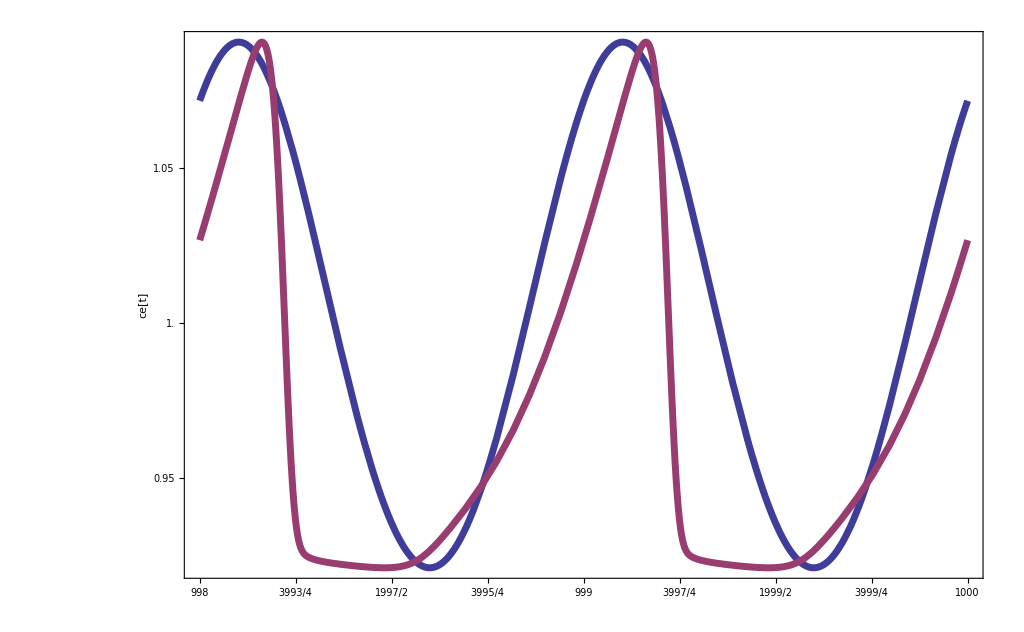

-Graphics-

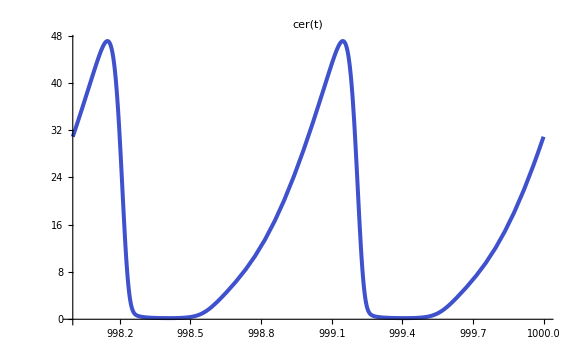
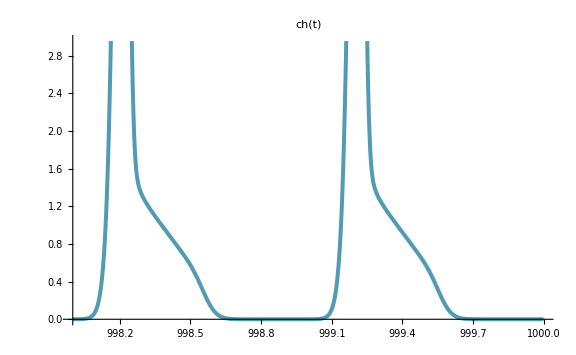
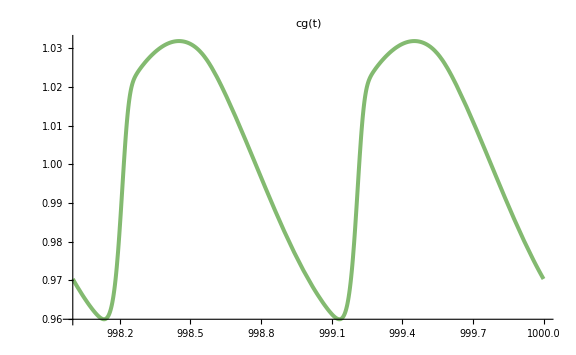
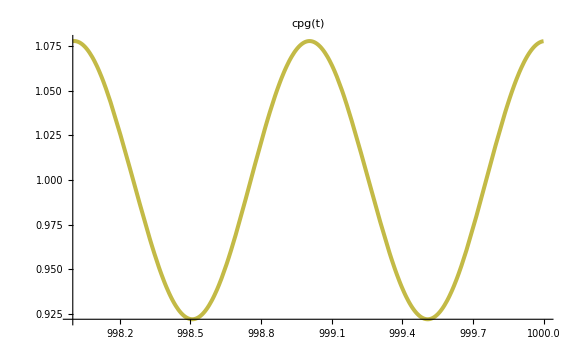
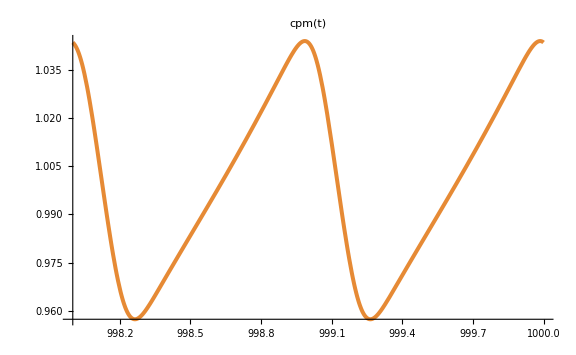
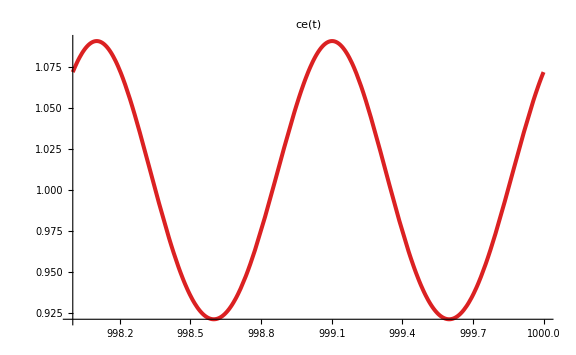

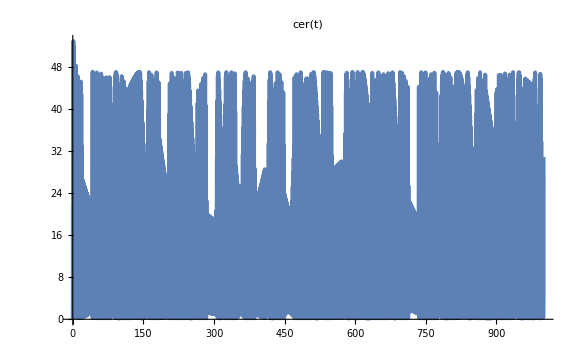
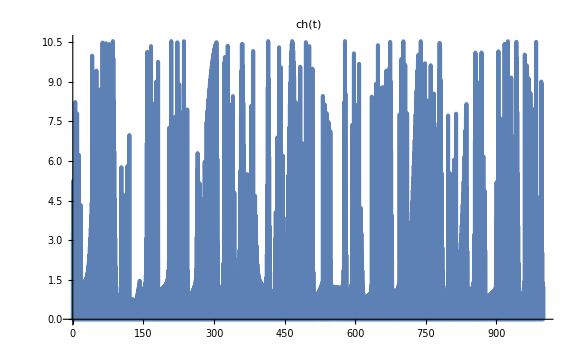

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {ndsol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$733438,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$733475,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partd: Part specification ndinputs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$733521,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$733546,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {ndsol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$394914,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$394950,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partd: Part specification ndinputs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$394998,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$395023,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {ndsol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$3688,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$3723,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partd: Part specification ndinputs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$3772,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$3797,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {ndsol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$9104,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$9205,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partd: Part specification ndinputs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$9251,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$9276,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {ndsol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$35664,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$35699,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partd: Part specification ndinputs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$35745,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$35770,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {ndsol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$67958,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$67993,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partd: Part specification ndinputs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$68039,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$68064,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {ndsol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$415869,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$415904,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partd: Part specification ndinputs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$415950,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$415975,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {ndsol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$17100,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$17135,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partd: Part specification ndinputs⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$49947,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$49972,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

ReplaceAll::reps: {ndsol⟦{}⟦1,1⟧⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$50045,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

Plot::plln: Limiting value ndtspan-48/scT in {Charting`Private`pvar$50080,ndtspan-48/scT,ndtspan} is not a machine-sized real number.

```mathematica
ndcevcint=TwoAxisPlot[{ce[t]/.ndsol[[Position[ndVars,ce[t]][[1,1]]]],Total[Table[ndVars[[i]]/.ndsol[[i]],{i,1,5}]]},{t,ndtspan-48/scT,ndtspan},{TextString[ce[t]],"Total intracellular c[t]"},ndtspan-(48-#)/scT&/@{0,6,12,18,24,30,36,42,48},GridLines->{ndtspan-(48-#)/scT&/@{0,6,12,18,24,30,36,42,48},None},PlotRangePadding->None]

Manipulate[Plot[Evaluate[var/.ndsol[[Position[ndVars,var][[1,1]]]]],{t,ndtspan-48/scT,ndtspan},ImageSize->Large,LabelStyle->Directive[18],PlotStyle->{Thickness[.005]},Ticks->{ndtspan-(48-#)/scT&/@{0,3,7,11,15,19,23,27,31,35,39,43,47},Automatic},GridLines->{Automatic,None},Frame->{{True,False},{True,False}},FrameLabel->{"CT","Concentration"},PlotLabel->ExpressionCell[ToString[TraditionalForm[dY[[Position[ndVars,var][[1,1]]]]]]<>"="<>ToString[TraditionalForm[dYdt[Position[ndVars,var][[1,1]]]]],PageWidth->400,TextAlignment->Center]],{var,ndVars}]

Manipulate[Plot[Evaluate[ndinputs[[inp]]],{t,ndtspan-48/scT,ndtspan},ImageSize->Large,LabelStyle->Directive[18],PlotStyle->{Thickness[.005]},GridLines->{Automatic,None},Frame->{{True,False},{True,False}},FrameLabel->{"CT","Concentration"},PlotLabel->ExpressionCell[TraditionalForm[ndinputs[[inp]]],PageWidth->400,TextAlignment->Center]],{inp,Range[Length[ndinputs]]}]

ndColPlotall2osc=ndcolPlotAll2osc=Plot[Evaluate[#/.ndsol[[Position[ndVars,#][[1,1]]]]&/@ndVars[[1;;5]]],{t,ndtspan-24*2/scT,ndtspan},PlotStyle->Flatten[{{Thickness[0.005],{ColorData["Rainbow"][#/6]}}&/@Range[5]},1],ImageSize->2^10,PlotLabels->Table[Style[ndVars[[i]],Bold,16,Purple],{i,1,Length[colVars]-1}],LabelStyle->Directive[18],Frame->{{True,False},{True,False}},FrameLabel->{Style["CT",Purple,Bold,40],Style["Concentration",Purple,Bold,40]},FrameTicks->{ndtspan-(48-#)/scT&/@{0,6,12,18,24,30,36,42,48},Automatic},GridLines->{ndtspan-(48-#)/scT&/@{0,6,12,18,24,30,36,42,48},None},PlotRangePadding->None]

ndcolPlots2osc=Table[Plot[ndVars[[i]]/.ndsol[[Position[ndVars,ndVars[[i]]][[1,1]]]],{t,ndtspan-24*2/scT,ndtspan},ImageSize->Large,PlotLabel->ndVars[[i]],LabelStyle->Directive[Bold,Purple],PlotStyle->{Thickness[.005],{ColorData["Rainbow"][i/6]}}],{i,Length[colVars]}]

ndvarPlotsAllTime=Table[Plot[ndVars[[i]]/.ndsol[[i]],{t,0,ndtspan},ImageSize->Large,PlotLabel->ndVars[[i]],LabelStyle->Directive[18],PlotStyle->{Thickness[.005]},PlotRange->All],{i,Length[ndVars]}]
```

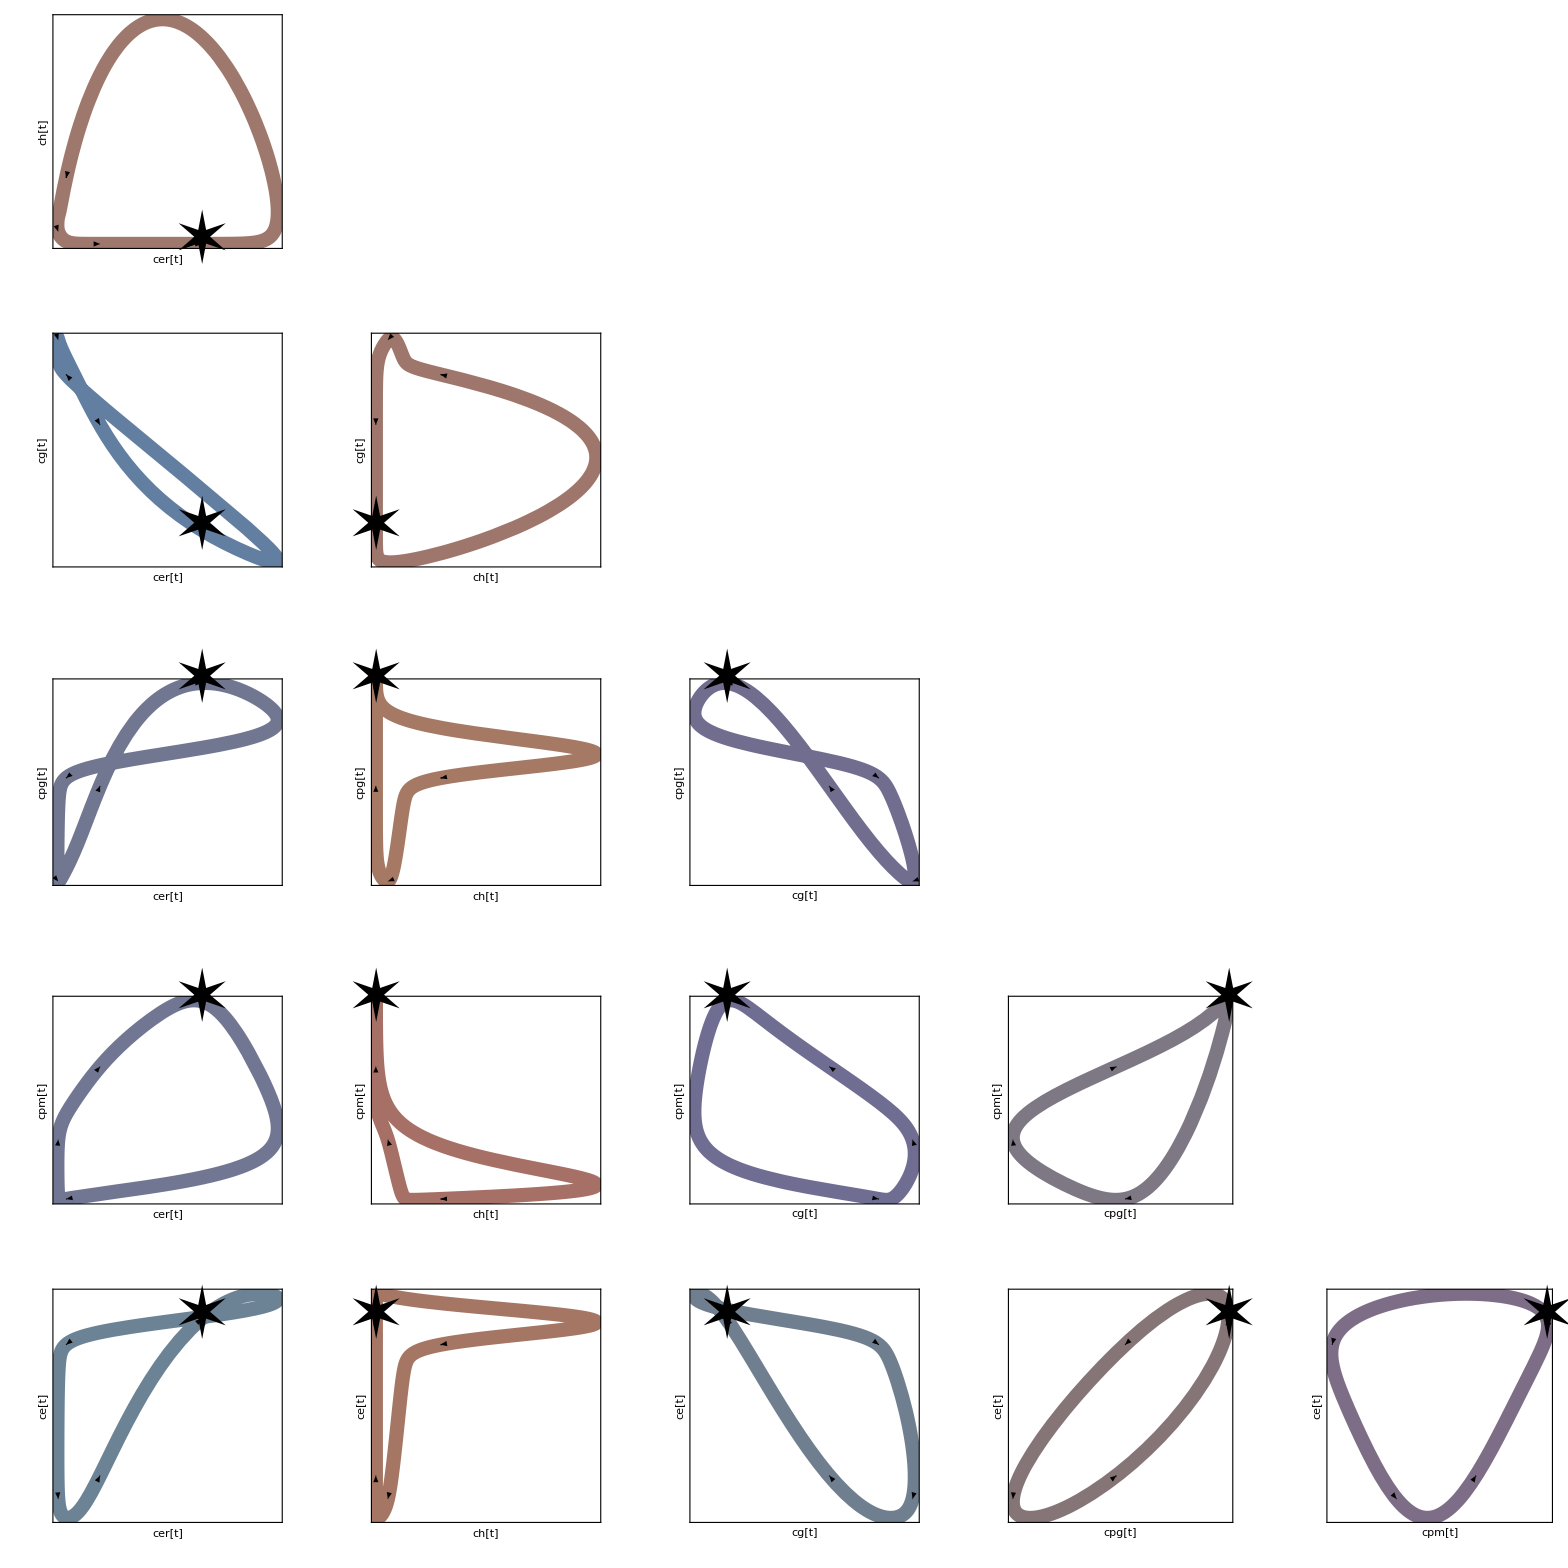

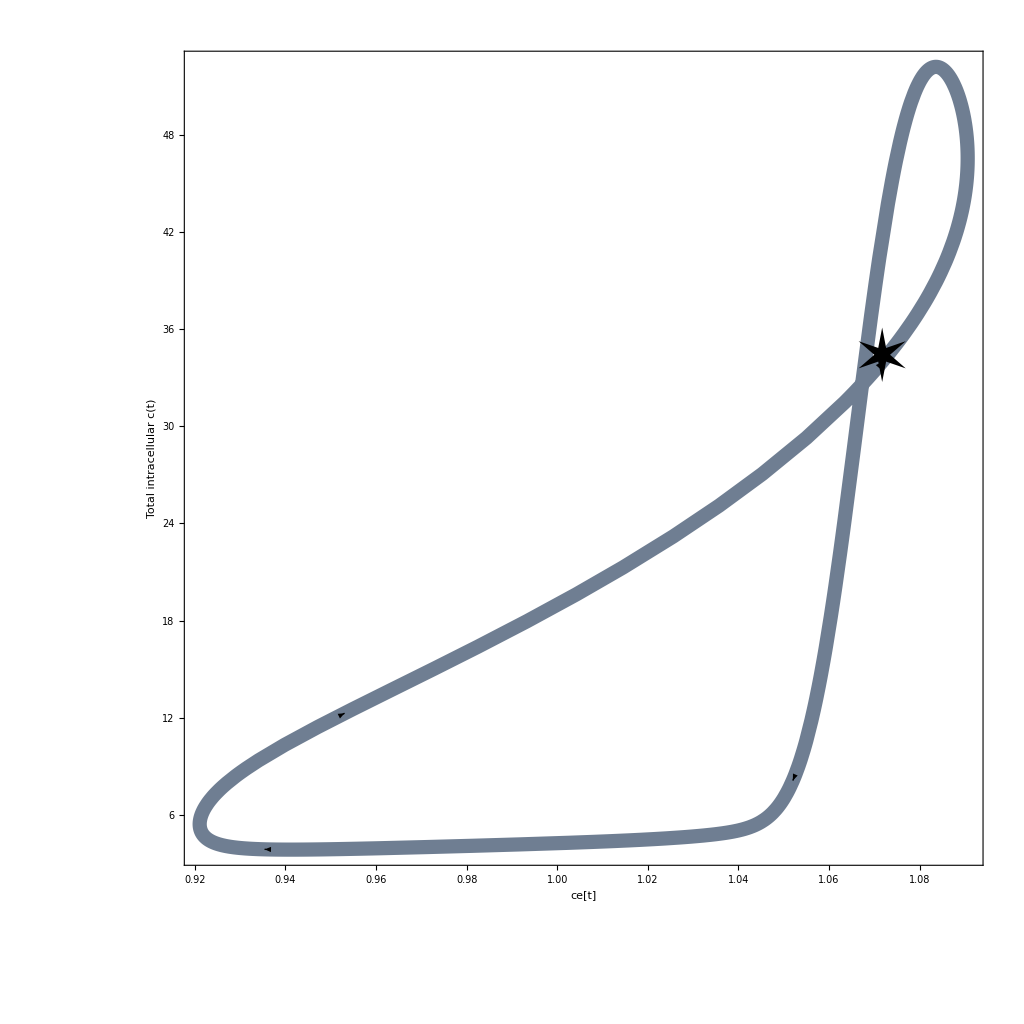

```mathematica
sfNDDy[x_]:=(x-Min[ndgradMin[[;;,1]]])/(Max[ndgradMax[[;;,1]]]-Min[ndgradMin[[;;,1]]])
ndparaColPlots=Table[Show[arrowParametricPlot[{ndVars[[i]]/.ndsol[[Position[ndVars,ndVars[[i]]][[1,1]]]],ndVars[[j]]/.ndsol[[Position[ndVars,ndVars[[j]]][[1,1]]]]},{t,ndtspan-24/scT,ndtspan},ImageSize->2^10,PlotStyle->{Thickness[.01]},ColorFunction->Function[{x,y,t},ColorData["Rainbow"][t]],AspectRatio->1,Frame->{{True,False},{True,False}},FrameTicks->None,FrameLabel->{Style[TextString[ndVars[[i]]],Purple,40,Bold],Style[TextString[ndVars[[j]]],Purple,40,Bold]}],Graphics[Text[Style["✶",144,Black],#]&/@{{ndVars[[i]]/.ndsol[[Position[ndVars,ndVars[[i]]][[1,1]]]],ndVars[[j]]/.ndsol[[Position[ndVars,ndVars[[j]]][[1,1]]]]}/.t->ndtspan-24/scT}]],{j,1,Length[colVars]},{i,1,Length[colVars]}];

ndparagrid=GraphicsGrid[Table[If[i>j,ndparaColPlots[[i,j]]],{i,2,Length[ndparaColPlots]},{j,1,Length[ndparaColPlots]-1}]]

ndpCEpCintphase=Show[arrowParametricPlot[{ce[t]/.ndsol[[Position[ndVars,ce[t]][[1,1]]]],Total[Table[ndVars[[i]]/.ndsol[[i]],{i,1,5}]]},{t,ndtspan-24/scT,ndtspan},ImageSize->2^10,AspectRatio->1,PlotStyle->{Thickness[.01]},ColorFunction->Function[{x,y,t},ColorData["Rainbow"][t]],Frame->{{True,False},{True,False}},FrameTicksStyle->Directive[Purple,24],FrameLabel->{Style[TextString[ce[t]],Purple,40,Bold],Style["Total intracellular c(t)",Purple,40,Bold]}],Graphics[Text[Style["✶",144,Black],#]&/@{{ce[t]/.ndsol[[Position[ndVars,ce[t]][[1,1]]]],Total[Table[ndVars[[i]]/.ndsol[[i]],{i,1,5}]]}/.t->ndtspan-24/scT}]]
```

```mathematica
Export["ND_params_t_scaling_"<>TextString[scT]<>".png",paramsBar,ImageResolution->200]
Export["ND_pCE_Cint_48_nofeed.png",ndcevcint,ImageResolution->200]
Export["ND_Cints_48_nofeedb.png",ndColPlotall2osc,ImageResolution->200]

Do[If[i≤j,Export["ND_phase_plot_"<>TextString[i]<>"_"<>TextString[j]<>"_pulse_nofeed.png",ndparaColPlots[[i,j]],ImageResolution->200]],{i,1,Length[ndparaColPlots]},{j,1,Length[ndparaColPlots]}];
Export["ND_pCintsPhase_pulse_nodiag_nofeed.png",ndparagrid,ImageResolution->80]
Export["ND_pCint_pCE_phase_pulse_nofeed.png",ndpCEpCintphase,ImageResolution->150]
```

ND_params_t_scaling_24.png

ND_pCE_Cint_48_nofeed.png

ND_Cints_48_nofeedb.png

ND_pCintsPhase_pulse_nodiag_nofeed.png

ND_pCint_pCE_phase_pulse_nofeed.png

## System stoichiometry

```mathematica
stoich=SparseArray[Join[#->1&/@{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,8},{7,10},{8,3},{9,12}},#->-1&/@{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,2},{7,9},{8,10},{8,11},{9,13}}]];
stoich//MatrixForm
RowReduce[stoich]//MatrixForm
```

(1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1)

## End - save space variables:

```mathematica
DumpSave["dump.mx","Global`"]
Now
```

{Global`}

Mon 4 Mar 2019 14:27:07GMT

```mathematica
(*SystemOpen[FileNameJoin[{$InstallationDirectory,"AddOns","Packages","EquationTrekker"}]]*)
```